# Differentiable SAT

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]]]
```

```mathematica
DAnd[x__]:=Min[x]
DOr[x__]:=Max[x]
DNot[x_]:=1-x
SoftenBooleanFunction[function_BooleanFunction]:=Module[{cnf,softBooleanFunction},
cnf=BooleanConvert[function,"CNF"];
softBooleanFunction=cnf//.{And->DAnd,Not->DNot,Or->DOr}
]
BooleanFunctionLayer[softBooleanFunction_Function,numVariables_]:=Module[
{
variableIndices=Range[numVariables],
variables
},
variables="B"<>ToString[#]&/@variableIndices;
NetGraph[
<|
"BooleanFunction"->FunctionLayer[Apply[softBooleanFunction]],
"Catenate"->CatenateLayer[],
Splice["B"<>ToString[#]->PartLayer[#]&/@variableIndices]
|>,
{
NetPort["Input"]->"Catenate",
"Catenate"->variables,
variables->"BooleanFunction"
}
]
]
VerifyFunctions[booleanFunction_BooleanFunction,softBooleanFunction_Function,booleanFunctionLayer_NetGraph,numVariables_]:=Module[
{inputs=Table[RandomChoice[{True,False},numVariables],20]},
ResourceFunction["DynamicMap"][{booleanFunction@@#,softBooleanFunction@@Boole[#],booleanFunctionLayer[Boole[#]]}&,inputs]
]
SoftBitsNet[size_,numVariables_]:=NetChain[
{
RandomBalancedNormalSoftBits[size],
(*InitializeBalanced[SoftBits[size]],*)
LinearLayer[size],
Tanh,
(*DropoutLayer[],*)
LinearLayer[numVariables],
Tanh,
(*DropoutLayer[],*)
ElementwiseLayer[(#+1)/2&]
}
]
DiffSATNet[booleanFunctionLayer_NetGraph,numVariables_]:=NetGraph[
<|
"SoftBits"->SoftBitsNet[100,numVariables],
"BooleanFunction"->booleanFunctionLayer
|>,
{"SoftBits"->"BooleanFunction"}
]
FindSATInstance[diffSATNet_NetGraph]:=Module[{},
NetTrain[diffSATNet,{1},All,ValidationSet->{1},MaxTrainingRounds->Infinity,TrainingStoppingCriterion->Function[#ValidationLoss<0.24],TargetDevice->"CPU"]
]
```

```mathematica
numVariables=20;
numFormulas=100;
formulas=ResourceFunction["DynamicMap"][BooleanFunction[#,numVariables]&,RandomInteger[{1,100000},numFormulas]];
```

```mathematica
formulaNum=RandomInteger[numFormulas];
booleanFunction=formulas[[formulaNum]];
SatisfiableQ[booleanFunction,Method->"SAT"]
```

True

```mathematica
softBooleanFunction=SoftenBooleanFunction[booleanFunction];
booleanFunctionLayer=BooleanFunctionLayer[softBooleanFunction,numVariables]
```

NetGraph[<>]

```mathematica
VerifyFunctions[booleanFunction,softBooleanFunction,booleanFunctionLayer,numVariables]
```

DynamicMap aborted at 40% after 4.4s, only 8 of 20 items were completed.

{{False,0,0.},{False,0,0.},{False,0,0.},{False,0,0.},{False,0,0.},{False,0,0.},{False,0,0.},{False,0,0.}}

```mathematica
diffSATNet=DiffSATNet[booleanFunctionLayer,numVariables]
```

NetGraph[<>]

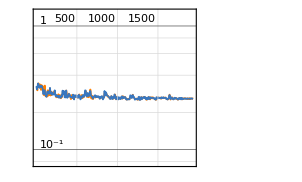
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1934  rounds:1934  time:1.4min  examples/s:23.
data | ,,  training examples:1  validation examples:1  processed examples:1934  skipped examples:0
method | ,,  ADAMoptimizer  batch size1CPU
round | ,,  loss:2.6×10^-1
validation | ,,  loss:2.51×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=FindSATInstance[diffSATNet]
```

```mathematica
sbn=NetInitialize[SoftBitsNet[100,2]]
```

NetChain[<>]

```mathematica
sbn[]
```

{0.553806,0.623446}

```mathematica
{trainedμ,trainedσ}=ExtractWeights[result["TrainedNet"]]
```

{{0.489591,0.488873,0.489355,0.489533,0.112872,0.488894,0.546693,0.83141,0.225312,0.530703},{-0.00533439,-0.000348017,-0.00242754,-0.00248427,0.110044,-0.00514757,0.1176,0.0537432,0.0889483,0.0787448}}

```mathematica
Column[Partition[Riffle[trainedμ,trainedσ],2]]
```

{0.489591,-0.00533439}
{0.488873,-0.000348017}
{0.489355,-0.00242754}
{0.489533,-0.00248427}
{0.112872,0.110044}
{0.488894,-0.00514757}
{0.546693,0.1176}
{0.83141,0.0537432}
{0.225312,0.0889483}
{0.530703,0.0787448}

```mathematica
formulas[[formulaNum]][False,False,False,False,False,False,False,False,True,False]
```

True

```mathematica
formulas[[formulaNum]][True,True,True,False,False,False,False,False,False,False]
```

False

```mathematica
SatisfiableQ[formulas[[2]],Method->"SAT"]
```

True